```mathematica
m[k_,τ_]:=m/.Solve[k==m*Exp[-m*τ],m][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

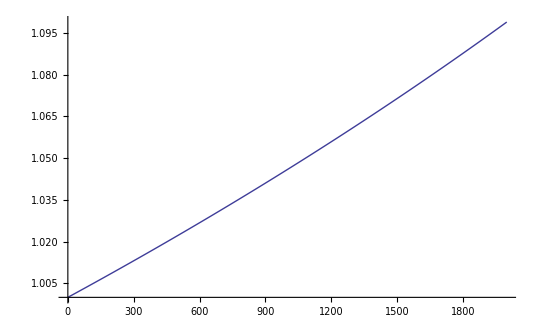

```mathematica
Plot[m[k,42.9*^-6]/k,{k,0,2000}]
```

```mathematica
Table[{k, m[k,42.9*^-6]/k},{k,0,2000,1}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,Indeterminate},{1,1.00004},{2,1.00009},{3,1.00013},{4,1.00017},{5,1.00021},{6,1.00026},{7,1.0003},{8,1.00034},{9,1.00039},{10,1.00043},{11,1.00047},{12,1.00052},{13,1.00056},{14,1.0006},{15,1.00064},{16,1.00069},{17,1.00073},{18,1.00077},{19,1.00082},{20,1.00086},{21,1.0009},{22,1.00095},{23,1.00099},{24,1.00103},{25,1.00107},{26,1.00112},{27,1.00116},{28,1.0012},{29,1.00125},{30,1.00129},{31,1.00133},{32,1.00138},{33,1.00142},{34,1.00146},{35,1.0015},{36,1.00155},{37,1.00159},{38,1.00163},{39,1.00168},{40,1.00172},{41,1.00176},{42,1.00181},{43,1.00185},{44,1.00189},{45,1.00194},{46,1.00198},{47,1.00202},{48,1.00207},{49,1.00211},{50,1.00215},{51,1.0022},{52,1.00224},{53,1.00228},{54,1.00232},{55,1.00237},{56,1.00241},{57,1.00245},{58,1.0025},{59,1.00254},{60,1.00258},{61,1.00263},{62,1.00267},{63,1.00271},{64,1.00276},{65,1.0028},{66,1.00284},{67,1.00289},{68,1.00293},{69,1.00297},{70,1.00302},{71,1.00306},{72,1.0031},{73,1.00315},{74,1.00319},{75,1.00323},{76,1.00328},{77,1.00332},{78,1.00336},{79,1.00341},{80,1.00345},{81,1.00349},{82,1.00354},{83,1.00358},{84,1.00362},{85,1.00367},{86,1.00371},{87,1.00375},{88,1.0038},{89,1.00384},{90,1.00388},{91,1.00393},{92,1.00397},{93,1.00401},{94,1.00406},{95,1.0041},{96,1.00414},{97,1.00419},{98,1.00423},{99,1.00427},{100,1.00432},{101,1.00436},{102,1.0044},{103,1.00445},{104,1.00449},{105,1.00454},{106,1.00458},{107,1.00462},{108,1.00467},{109,1.00471},{110,1.00475},{111,1.0048},{112,1.00484},{113,1.00488},{114,1.00493},{115,1.00497},{116,1.00501},{117,1.00506},{118,1.0051},{119,1.00514},{120,1.00519},{121,1.00523},{122,1.00528},{123,1.00532},{124,1.00536},{125,1.00541},{126,1.00545},{127,1.00549},{128,1.00554},{129,1.00558},{130,1.00562},{131,1.00567},{132,1.00571},{133,1.00576},{134,1.0058},{135,1.00584},{136,1.00589},{137,1.00593},{138,1.00597},{139,1.00602},{140,1.00606},{141,1.0061},{142,1.00615},{143,1.00619},{144,1.00624},{145,1.00628},{146,1.00632},{147,1.00637},{148,1.00641},{149,1.00645},{150,1.0065},{151,1.00654},{152,1.00659},{153,1.00663},{154,1.00667},{155,1.00672},{156,1.00676},{157,1.0068},{158,1.00685},{159,1.00689},{160,1.00694},{161,1.00698},{162,1.00702},{163,1.00707},{164,1.00711},{165,1.00715},{166,1.0072},{167,1.00724},{168,1.00729},{169,1.00733},{170,1.00737},{171,1.00742},{172,1.00746},{173,1.00751},{174,1.00755},{175,1.00759},{176,1.00764},{177,1.00768},{178,1.00772},{179,1.00777},{180,1.00781},{181,1.00786},{182,1.0079},{183,1.00794},{184,1.00799},{185,1.00803},{186,1.00808},{187,1.00812},{188,1.00816},{189,1.00821},{190,1.00825},{191,1.0083},{192,1.00834},{193,1.00838},{194,1.00843},{195,1.00847},{196,1.00852},{197,1.00856},{198,1.0086},{199,1.00865},{200,1.00869},{201,1.00874},{202,1.00878},{203,1.00882},{204,1.00887},{205,1.00891},{206,1.00896},{207,1.009},{208,1.00904},{209,1.00909},{210,1.00913},{211,1.00918},{212,1.00922},{213,1.00927},{214,1.00931},{215,1.00935},{216,1.0094},{217,1.00944},{218,1.00949},{219,1.00953},{220,1.00957},{221,1.00962},{222,1.00966},{223,1.00971},{224,1.00975},{225,1.00979},{226,1.00984},{227,1.00988},{228,1.00993},{229,1.00997},{230,1.01002},{231,1.01006},{232,1.0101},{233,1.01015},{234,1.01019},{235,1.01024},{236,1.01028},{237,1.01033},{238,1.01037},{239,1.01041},{240,1.01046},{241,1.0105},{242,1.01055},{243,1.01059},{244,1.01064},{245,1.01068},{246,1.01072},{247,1.01077},{248,1.01081},{249,1.01086},{250,1.0109},{251,1.01095},{252,1.01099},{253,1.01103},{254,1.01108},{255,1.01112},{256,1.01117},{257,1.01121},{258,1.01126},{259,1.0113},{260,1.01134},{261,1.01139},{262,1.01143},{263,1.01148},{264,1.01152},{265,1.01157},{266,1.01161},{267,1.01166},{268,1.0117},{269,1.01174},{270,1.01179},{271,1.01183},{272,1.01188},{273,1.01192},{274,1.01197},{275,1.01201},{276,1.01206},{277,1.0121},{278,1.01214},{279,1.01219},{280,1.01223},{281,1.01228},{282,1.01232},{283,1.01237},{284,1.01241},{285,1.01246},{286,1.0125},{287,1.01254},{288,1.01259},{289,1.01263},{290,1.01268},{291,1.01272},{292,1.01277},{293,1.01281},{294,1.01286},{295,1.0129},{296,1.01295},{297,1.01299},{298,1.01304},{299,1.01308},{300,1.01312},{301,1.01317},{302,1.01321},{303,1.01326},{304,1.0133},{305,1.01335},{306,1.01339},{307,1.01344},{308,1.01348},{309,1.01353},{310,1.01357},{311,1.01362},{312,1.01366},{313,1.0137},{314,1.01375},{315,1.01379},{316,1.01384},{317,1.01388},{318,1.01393},{319,1.01397},{320,1.01402},{321,1.01406},{322,1.01411},{323,1.01415},{324,1.0142},{325,1.01424},{326,1.01429},{327,1.01433},{328,1.01438},{329,1.01442},{330,1.01447},{331,1.01451},{332,1.01456},{333,1.0146},{334,1.01464},{335,1.01469},{336,1.01473},{337,1.01478},{338,1.01482},{339,1.01487},{340,1.01491},{341,1.01496},{342,1.015},{343,1.01505},{344,1.01509},{345,1.01514},{346,1.01518},{347,1.01523},{348,1.01527},{349,1.01532},{350,1.01536},{351,1.01541},{352,1.01545},{353,1.0155},{354,1.01554},{355,1.01559},{356,1.01563},{357,1.01568},{358,1.01572},{359,1.01577},{360,1.01581},{361,1.01586},{362,1.0159},{363,1.01595},{364,1.01599},{365,1.01604},{366,1.01608},{367,1.01613},{368,1.01617},{369,1.01622},{370,1.01626},{371,1.01631},{372,1.01635},{373,1.0164},{374,1.01644},{375,1.01649},{376,1.01653},{377,1.01658},{378,1.01662},{379,1.01667},{380,1.01671},{381,1.01676},{382,1.0168},{383,1.01685},{384,1.01689},{385,1.01694},{386,1.01698},{387,1.01703},{388,1.01707},{389,1.01712},{390,1.01716},{391,1.01721},{392,1.01725},{393,1.0173},{394,1.01734},{395,1.01739},{396,1.01743},{397,1.01748},{398,1.01753},{399,1.01757},{400,1.01762},{401,1.01766},{402,1.01771},{403,1.01775},{404,1.0178},{405,1.01784},{406,1.01789},{407,1.01793},{408,1.01798},{409,1.01802},{410,1.01807},{411,1.01811},{412,1.01816},{413,1.0182},{414,1.01825},{415,1.01829},{416,1.01834},{417,1.01839},{418,1.01843},{419,1.01848},{420,1.01852},{421,1.01857},{422,1.01861},{423,1.01866},{424,1.0187},{425,1.01875},{426,1.01879},{427,1.01884},{428,1.01888},{429,1.01893},{430,1.01897},{431,1.01902},{432,1.01907},{433,1.01911},{434,1.01916},{435,1.0192},{436,1.01925},{437,1.01929},{438,1.01934},{439,1.01938},{440,1.01943},{441,1.01947},{442,1.01952},{443,1.01957},{444,1.01961},{445,1.01966},{446,1.0197},{447,1.01975},{448,1.01979},{449,1.01984},{450,1.01988},{451,1.01993},{452,1.01998},{453,1.02002},{454,1.02007},{455,1.02011},{456,1.02016},{457,1.0202},{458,1.02025},{459,1.02029},{460,1.02034},{461,1.02039},{462,1.02043},{463,1.02048},{464,1.02052},{465,1.02057},{466,1.02061},{467,1.02066},{468,1.0207},{469,1.02075},{470,1.0208},{471,1.02084},{472,1.02089},{473,1.02093},{474,1.02098},{475,1.02102},{476,1.02107},{477,1.02112},{478,1.02116},{479,1.02121},{480,1.02125},{481,1.0213},{482,1.02134},{483,1.02139},{484,1.02144},{485,1.02148},{486,1.02153},{487,1.02157},{488,1.02162},{489,1.02166},{490,1.02171},{491,1.02176},{492,1.0218},{493,1.02185},{494,1.02189},{495,1.02194},{496,1.02198},{497,1.02203},{498,1.02208},{499,1.02212},{500,1.02217},{501,1.02221},{502,1.02226},{503,1.02231},{504,1.02235},{505,1.0224},{506,1.02244},{507,1.02249},{508,1.02253},{509,1.02258},{510,1.02263},{511,1.02267},{512,1.02272},{513,1.02276},{514,1.02281},{515,1.02286},{516,1.0229},{517,1.02295},{518,1.02299},{519,1.02304},{520,1.02309},{521,1.02313},{522,1.02318},{523,1.02322},{524,1.02327},{525,1.02332},{526,1.02336},{527,1.02341},{528,1.02345},{529,1.0235},{530,1.02355},{531,1.02359},{532,1.02364},{533,1.02368},{534,1.02373},{535,1.02378},{536,1.02382},{537,1.02387},{538,1.02391},{539,1.02396},{540,1.02401},{541,1.02405},{542,1.0241},{543,1.02414},{544,1.02419},{545,1.02424},{546,1.02428},{547,1.02433},{548,1.02437},{549,1.02442},{550,1.02447},{551,1.02451},{552,1.02456},{553,1.02461},{554,1.02465},{555,1.0247},{556,1.02474},{557,1.02479},{558,1.02484},{559,1.02488},{560,1.02493},{561,1.02497},{562,1.02502},{563,1.02507},{564,1.02511},{565,1.02516},{566,1.02521},{567,1.02525},{568,1.0253},{569,1.02534},{570,1.02539},{571,1.02544},{572,1.02548},{573,1.02553},{574,1.02558},{575,1.02562},{576,1.02567},{577,1.02571},{578,1.02576},{579,1.02581},{580,1.02585},{581,1.0259},{582,1.02595},{583,1.02599},{584,1.02604},{585,1.02609},{586,1.02613},{587,1.02618},{588,1.02622},{589,1.02627},{590,1.02632},{591,1.02636},{592,1.02641},{593,1.02646},{594,1.0265},{595,1.02655},{596,1.0266},{597,1.02664},{598,1.02669},{599,1.02674},{600,1.02678},{601,1.02683},{602,1.02687},{603,1.02692},{604,1.02697},{605,1.02701},{606,1.02706},{607,1.02711},{608,1.02715},{609,1.0272},{610,1.02725},{611,1.02729},{612,1.02734},{613,1.02739},{614,1.02743},{615,1.02748},{616,1.02753},{617,1.02757},{618,1.02762},{619,1.02767},{620,1.02771},{621,1.02776},{622,1.02781},{623,1.02785},{624,1.0279},{625,1.02795},{626,1.02799},{627,1.02804},{628,1.02808},{629,1.02813},{630,1.02818},{631,1.02822},{632,1.02827},{633,1.02832},{634,1.02836},{635,1.02841},{636,1.02846},{637,1.0285},{638,1.02855},{639,1.0286},{640,1.02865},{641,1.02869},{642,1.02874},{643,1.02879},{644,1.02883},{645,1.02888},{646,1.02893},{647,1.02897},{648,1.02902},{649,1.02907},{650,1.02911},{651,1.02916},{652,1.02921},{653,1.02925},{654,1.0293},{655,1.02935},{656,1.02939},{657,1.02944},{658,1.02949},{659,1.02953},{660,1.02958},{661,1.02963},{662,1.02967},{663,1.02972},{664,1.02977},{665,1.02981},{666,1.02986},{667,1.02991},{668,1.02996},{669,1.03},{670,1.03005},{671,1.0301},{672,1.03014},{673,1.03019},{674,1.03024},{675,1.03028},{676,1.03033},{677,1.03038},{678,1.03042},{679,1.03047},{680,1.03052},{681,1.03057},{682,1.03061},{683,1.03066},{684,1.03071},{685,1.03075},{686,1.0308},{687,1.03085},{688,1.03089},{689,1.03094},{690,1.03099},{691,1.03104},{692,1.03108},{693,1.03113},{694,1.03118},{695,1.03122},{696,1.03127},{697,1.03132},{698,1.03137},{699,1.03141},{700,1.03146},{701,1.03151},{702,1.03155},{703,1.0316},{704,1.03165},{705,1.0317},{706,1.03174},{707,1.03179},{708,1.03184},{709,1.03188},{710,1.03193},{711,1.03198},{712,1.03203},{713,1.03207},{714,1.03212},{715,1.03217},{716,1.03221},{717,1.03226},{718,1.03231},{719,1.03236},{720,1.0324},{721,1.03245},{722,1.0325},{723,1.03254},{724,1.03259},{725,1.03264},{726,1.03269},{727,1.03273},{728,1.03278},{729,1.03283},{730,1.03288},{731,1.03292},{732,1.03297},{733,1.03302},{734,1.03306},{735,1.03311},{736,1.03316},{737,1.03321},{738,1.03325},{739,1.0333},{740,1.03335},{741,1.0334},{742,1.03344},{743,1.03349},{744,1.03354},{745,1.03359},{746,1.03363},{747,1.03368},{748,1.03373},{749,1.03378},{750,1.03382},{751,1.03387},{752,1.03392},{753,1.03396},{754,1.03401},{755,1.03406},{756,1.03411},{757,1.03415},{758,1.0342},{759,1.03425},{760,1.0343},{761,1.03434},{762,1.03439},{763,1.03444},{764,1.03449},{765,1.03453},{766,1.03458},{767,1.03463},{768,1.03468},{769,1.03472},{770,1.03477},{771,1.03482},{772,1.03487},{773,1.03492},{774,1.03496},{775,1.03501},{776,1.03506},{777,1.03511},{778,1.03515},{779,1.0352},{780,1.03525},{781,1.0353},{782,1.03534},{783,1.03539},{784,1.03544},{785,1.03549},{786,1.03553},{787,1.03558},{788,1.03563},{789,1.03568},{790,1.03573},{791,1.03577},{792,1.03582},{793,1.03587},{794,1.03592},{795,1.03596},{796,1.03601},{797,1.03606},{798,1.03611},{799,1.03615},{800,1.0362},{801,1.03625},{802,1.0363},{803,1.03635},{804,1.03639},{805,1.03644},{806,1.03649},{807,1.03654},{808,1.03658},{809,1.03663},{810,1.03668},{811,1.03673},{812,1.03678},{813,1.03682},{814,1.03687},{815,1.03692},{816,1.03697},{817,1.03702},{818,1.03706},{819,1.03711},{820,1.03716},{821,1.03721},{822,1.03725},{823,1.0373},{824,1.03735},{825,1.0374},{826,1.03745},{827,1.03749},{828,1.03754},{829,1.03759},{830,1.03764},{831,1.03769},{832,1.03773},{833,1.03778},{834,1.03783},{835,1.03788},{836,1.03793},{837,1.03797},{838,1.03802},{839,1.03807},{840,1.03812},{841,1.03817},{842,1.03821},{843,1.03826},{844,1.03831},{845,1.03836},{846,1.03841},{847,1.03845},{848,1.0385},{849,1.03855},{850,1.0386},{851,1.03865},{852,1.0387},{853,1.03874},{854,1.03879},{855,1.03884},{856,1.03889},{857,1.03894},{858,1.03898},{859,1.03903},{860,1.03908},{861,1.03913},{862,1.03918},{863,1.03922},{864,1.03927},{865,1.03932},{866,1.03937},{867,1.03942},{868,1.03947},{869,1.03951},{870,1.03956},{871,1.03961},{872,1.03966},{873,1.03971},{874,1.03976},{875,1.0398},{876,1.03985},{877,1.0399},{878,1.03995},{879,1.04},{880,1.04004},{881,1.04009},{882,1.04014},{883,1.04019},{884,1.04024},{885,1.04029},{886,1.04033},{887,1.04038},{888,1.04043},{889,1.04048},{890,1.04053},{891,1.04058},{892,1.04062},{893,1.04067},{894,1.04072},{895,1.04077},{896,1.04082},{897,1.04087},{898,1.04092},{899,1.04096},{900,1.04101},{901,1.04106},{902,1.04111},{903,1.04116},{904,1.04121},{905,1.04125},{906,1.0413},{907,1.04135},{908,1.0414},{909,1.04145},{910,1.0415},{911,1.04155},{912,1.04159},{913,1.04164},{914,1.04169},{915,1.04174},{916,1.04179},{917,1.04184},{918,1.04189},{919,1.04193},{920,1.04198},{921,1.04203},{922,1.04208},{923,1.04213},{924,1.04218},{925,1.04223},{926,1.04227},{927,1.04232},{928,1.04237},{929,1.04242},{930,1.04247},{931,1.04252},{932,1.04257},{933,1.04261},{934,1.04266},{935,1.04271},{936,1.04276},{937,1.04281},{938,1.04286},{939,1.04291},{940,1.04296},{941,1.043},{942,1.04305},{943,1.0431},{944,1.04315},{945,1.0432},{946,1.04325},{947,1.0433},{948,1.04335},{949,1.04339},{950,1.04344},{951,1.04349},{952,1.04354},{953,1.04359},{954,1.04364},{955,1.04369},{956,1.04374},{957,1.04378},{958,1.04383},{959,1.04388},{960,1.04393},{961,1.04398},{962,1.04403},{963,1.04408},{964,1.04413},{965,1.04418},{966,1.04422},{967,1.04427},{968,1.04432},{969,1.04437},{970,1.04442},{971,1.04447},{972,1.04452},{973,1.04457},{974,1.04462},{975,1.04466},{976,1.04471},{977,1.04476},{978,1.04481},{979,1.04486},{980,1.04491},{981,1.04496},{982,1.04501},{983,1.04506},{984,1.04511},{985,1.04515},{986,1.0452},{987,1.04525},{988,1.0453},{989,1.04535},{990,1.0454},{991,1.04545},{992,1.0455},{993,1.04555},{994,1.0456},{995,1.04564},{996,1.04569},{997,1.04574},{998,1.04579},{999,1.04584},{1000,1.04589},{1001,1.04594},{1002,1.04599},{1003,1.04604},{1004,1.04609},{1005,1.04614},{1006,1.04619},{1007,1.04623},{1008,1.04628},{1009,1.04633},{1010,1.04638},{1011,1.04643},{1012,1.04648},{1013,1.04653},{1014,1.04658},{1015,1.04663},{1016,1.04668},{1017,1.04673},{1018,1.04678},{1019,1.04683},{1020,1.04687},{1021,1.04692},{1022,1.04697},{1023,1.04702},{1024,1.04707},{1025,1.04712},{1026,1.04717},{1027,1.04722},{1028,1.04727},{1029,1.04732},{1030,1.04737},{1031,1.04742},{1032,1.04747},{1033,1.04752},{1034,1.04757},{1035,1.04761},{1036,1.04766},{1037,1.04771},{1038,1.04776},{1039,1.04781},{1040,1.04786},{1041,1.04791},{1042,1.04796},{1043,1.04801},{1044,1.04806},{1045,1.04811},{1046,1.04816},{1047,1.04821},{1048,1.04826},{1049,1.04831},{1050,1.04836},{1051,1.04841},{1052,1.04845},{1053,1.0485},{1054,1.04855},{1055,1.0486},{1056,1.04865},{1057,1.0487},{1058,1.04875},{1059,1.0488},{1060,1.04885},{1061,1.0489},{1062,1.04895},{1063,1.049},{1064,1.04905},{1065,1.0491},{1066,1.04915},{1067,1.0492},{1068,1.04925},{1069,1.0493},{1070,1.04935},{1071,1.0494},{1072,1.04945},{1073,1.0495},{1074,1.04955},{1075,1.0496},{1076,1.04965},{1077,1.04969},{1078,1.04974},{1079,1.04979},{1080,1.04984},{1081,1.04989},{1082,1.04994},{1083,1.04999},{1084,1.05004},{1085,1.05009},{1086,1.05014},{1087,1.05019},{1088,1.05024},{1089,1.05029},{1090,1.05034},{1091,1.05039},{1092,1.05044},{1093,1.05049},{1094,1.05054},{1095,1.05059},{1096,1.05064},{1097,1.05069},{1098,1.05074},{1099,1.05079},{1100,1.05084},{1101,1.05089},{1102,1.05094},{1103,1.05099},{1104,1.05104},{1105,1.05109},{1106,1.05114},{1107,1.05119},{1108,1.05124},{1109,1.05129},{1110,1.05134},{1111,1.05139},{1112,1.05144},{1113,1.05149},{1114,1.05154},{1115,1.05159},{1116,1.05164},{1117,1.05169},{1118,1.05174},{1119,1.05179},{1120,1.05184},{1121,1.05189},{1122,1.05194},{1123,1.05199},{1124,1.05204},{1125,1.05209},{1126,1.05214},{1127,1.05219},{1128,1.05224},{1129,1.05229},{1130,1.05234},{1131,1.05239},{1132,1.05244},{1133,1.05249},{1134,1.05254},{1135,1.05259},{1136,1.05264},{1137,1.05269},{1138,1.05274},{1139,1.05279},{1140,1.05284},{1141,1.05289},{1142,1.05294},{1143,1.05299},{1144,1.05304},{1145,1.05309},{1146,1.05314},{1147,1.05319},{1148,1.05324},{1149,1.05329},{1150,1.05334},{1151,1.05339},{1152,1.05344},{1153,1.05349},{1154,1.05354},{1155,1.05359},{1156,1.05364},{1157,1.05369},{1158,1.05374},{1159,1.05379},{1160,1.05384},{1161,1.05389},{1162,1.05394},{1163,1.05399},{1164,1.05404},{1165,1.05409},{1166,1.05414},{1167,1.0542},{1168,1.05425},{1169,1.0543},{1170,1.05435},{1171,1.0544},{1172,1.05445},{1173,1.0545},{1174,1.05455},{1175,1.0546},{1176,1.05465},{1177,1.0547},{1178,1.05475},{1179,1.0548},{1180,1.05485},{1181,1.0549},{1182,1.05495},{1183,1.055},{1184,1.05505},{1185,1.0551},{1186,1.05515},{1187,1.0552},{1188,1.05525},{1189,1.0553},{1190,1.05535},{1191,1.05541},{1192,1.05546},{1193,1.05551},{1194,1.05556},{1195,1.05561},{1196,1.05566},{1197,1.05571},{1198,1.05576},{1199,1.05581},{1200,1.05586},{1201,1.05591},{1202,1.05596},{1203,1.05601},{1204,1.05606},{1205,1.05611},{1206,1.05616},{1207,1.05621},{1208,1.05626},{1209,1.05632},{1210,1.05637},{1211,1.05642},{1212,1.05647},{1213,1.05652},{1214,1.05657},{1215,1.05662},{1216,1.05667},{1217,1.05672},{1218,1.05677},{1219,1.05682},{1220,1.05687},{1221,1.05692},{1222,1.05697},{1223,1.05703},{1224,1.05708},{1225,1.05713},{1226,1.05718},{1227,1.05723},{1228,1.05728},{1229,1.05733},{1230,1.05738},{1231,1.05743},{1232,1.05748},{1233,1.05753},{1234,1.05758},{1235,1.05763},{1236,1.05769},{1237,1.05774},{1238,1.05779},{1239,1.05784},{1240,1.05789},{1241,1.05794},{1242,1.05799},{1243,1.05804},{1244,1.05809},{1245,1.05814},{1246,1.05819},{1247,1.05825},{1248,1.0583},{1249,1.05835},{1250,1.0584},{1251,1.05845},{1252,1.0585},{1253,1.05855},{1254,1.0586},{1255,1.05865},{1256,1.0587},{1257,1.05875},{1258,1.05881},{1259,1.05886},{1260,1.05891},{1261,1.05896},{1262,1.05901},{1263,1.05906},{1264,1.05911},{1265,1.05916},{1266,1.05921},{1267,1.05927},{1268,1.05932},{1269,1.05937},{1270,1.05942},{1271,1.05947},{1272,1.05952},{1273,1.05957},{1274,1.05962},{1275,1.05967},{1276,1.05973},{1277,1.05978},{1278,1.05983},{1279,1.05988},{1280,1.05993},{1281,1.05998},{1282,1.06003},{1283,1.06008},{1284,1.06013},{1285,1.06019},{1286,1.06024},{1287,1.06029},{1288,1.06034},{1289,1.06039},{1290,1.06044},{1291,1.06049},{1292,1.06054},{1293,1.0606},{1294,1.06065},{1295,1.0607},{1296,1.06075},{1297,1.0608},{1298,1.06085},{1299,1.0609},{1300,1.06096},{1301,1.06101},{1302,1.06106},{1303,1.06111},{1304,1.06116},{1305,1.06121},{1306,1.06126},{1307,1.06131},{1308,1.06137},{1309,1.06142},{1310,1.06147},{1311,1.06152},{1312,1.06157},{1313,1.06162},{1314,1.06167},{1315,1.06173},{1316,1.06178},{1317,1.06183},{1318,1.06188},{1319,1.06193},{1320,1.06198},{1321,1.06203},{1322,1.06209},{1323,1.06214},{1324,1.06219},{1325,1.06224},{1326,1.06229},{1327,1.06234},{1328,1.0624},{1329,1.06245},{1330,1.0625},{1331,1.06255},{1332,1.0626},{1333,1.06265},{1334,1.0627},{1335,1.06276},{1336,1.06281},{1337,1.06286},{1338,1.06291},{1339,1.06296},{1340,1.06301},{1341,1.06307},{1342,1.06312},{1343,1.06317},{1344,1.06322},{1345,1.06327},{1346,1.06332},{1347,1.06338},{1348,1.06343},{1349,1.06348},{1350,1.06353},{1351,1.06358},{1352,1.06363},{1353,1.06369},{1354,1.06374},{1355,1.06379},{1356,1.06384},{1357,1.06389},{1358,1.06394},{1359,1.064},{1360,1.06405},{1361,1.0641},{1362,1.06415},{1363,1.0642},{1364,1.06426},{1365,1.06431},{1366,1.06436},{1367,1.06441},{1368,1.06446},{1369,1.06451},{1370,1.06457},{1371,1.06462},{1372,1.06467},{1373,1.06472},{1374,1.06477},{1375,1.06483},{1376,1.06488},{1377,1.06493},{1378,1.06498},{1379,1.06503},{1380,1.06509},{1381,1.06514},{1382,1.06519},{1383,1.06524},{1384,1.06529},{1385,1.06535},{1386,1.0654},{1387,1.06545},{1388,1.0655},{1389,1.06555},{1390,1.06561},{1391,1.06566},{1392,1.06571},{1393,1.06576},{1394,1.06581},{1395,1.06587},{1396,1.06592},{1397,1.06597},{1398,1.06602},{1399,1.06607},{1400,1.06613},{1401,1.06618},{1402,1.06623},{1403,1.06628},{1404,1.06633},{1405,1.06639},{1406,1.06644},{1407,1.06649},{1408,1.06654},{1409,1.0666},{1410,1.06665},{1411,1.0667},{1412,1.06675},{1413,1.0668},{1414,1.06686},{1415,1.06691},{1416,1.06696},{1417,1.06701},{1418,1.06707},{1419,1.06712},{1420,1.06717},{1421,1.06722},{1422,1.06727},{1423,1.06733},{1424,1.06738},{1425,1.06743},{1426,1.06748},{1427,1.06754},{1428,1.06759},{1429,1.06764},{1430,1.06769},{1431,1.06774},{1432,1.0678},{1433,1.06785},{1434,1.0679},{1435,1.06795},{1436,1.06801},{1437,1.06806},{1438,1.06811},{1439,1.06816},{1440,1.06822},{1441,1.06827},{1442,1.06832},{1443,1.06837},{1444,1.06843},{1445,1.06848},{1446,1.06853},{1447,1.06858},{1448,1.06864},{1449,1.06869},{1450,1.06874},{1451,1.06879},{1452,1.06885},{1453,1.0689},{1454,1.06895},{1455,1.069},{1456,1.06906},{1457,1.06911},{1458,1.06916},{1459,1.06921},{1460,1.06927},{1461,1.06932},{1462,1.06937},{1463,1.06942},{1464,1.06948},{1465,1.06953},{1466,1.06958},{1467,1.06963},{1468,1.06969},{1469,1.06974},{1470,1.06979},{1471,1.06984},{1472,1.0699},{1473,1.06995},{1474,1.07},{1475,1.07006},{1476,1.07011},{1477,1.07016},{1478,1.07021},{1479,1.07027},{1480,1.07032},{1481,1.07037},{1482,1.07042},{1483,1.07048},{1484,1.07053},{1485,1.07058},{1486,1.07064},{1487,1.07069},{1488,1.07074},{1489,1.07079},{1490,1.07085},{1491,1.0709},{1492,1.07095},{1493,1.07101},{1494,1.07106},{1495,1.07111},{1496,1.07116},{1497,1.07122},{1498,1.07127},{1499,1.07132},{1500,1.07138},{1501,1.07143},{1502,1.07148},{1503,1.07153},{1504,1.07159},{1505,1.07164},{1506,1.07169},{1507,1.07175},{1508,1.0718},{1509,1.07185},{1510,1.0719},{1511,1.07196},{1512,1.07201},{1513,1.07206},{1514,1.07212},{1515,1.07217},{1516,1.07222},{1517,1.07228},{1518,1.07233},{1519,1.07238},{1520,1.07243},{1521,1.07249},{1522,1.07254},{1523,1.07259},{1524,1.07265},{1525,1.0727},{1526,1.07275},{1527,1.07281},{1528,1.07286},{1529,1.07291},{1530,1.07297},{1531,1.07302},{1532,1.07307},{1533,1.07312},{1534,1.07318},{1535,1.07323},{1536,1.07328},{1537,1.07334},{1538,1.07339},{1539,1.07344},{1540,1.0735},{1541,1.07355},{1542,1.0736},{1543,1.07366},{1544,1.07371},{1545,1.07376},{1546,1.07382},{1547,1.07387},{1548,1.07392},{1549,1.07398},{1550,1.07403},{1551,1.07408},{1552,1.07414},{1553,1.07419},{1554,1.07424},{1555,1.0743},{1556,1.07435},{1557,1.0744},{1558,1.07446},{1559,1.07451},{1560,1.07456},{1561,1.07462},{1562,1.07467},{1563,1.07472},{1564,1.07478},{1565,1.07483},{1566,1.07488},{1567,1.07494},{1568,1.07499},{1569,1.07504},{1570,1.0751},{1571,1.07515},{1572,1.0752},{1573,1.07526},{1574,1.07531},{1575,1.07536},{1576,1.07542},{1577,1.07547},{1578,1.07553},{1579,1.07558},{1580,1.07563},{1581,1.07569},{1582,1.07574},{1583,1.07579},{1584,1.07585},{1585,1.0759},{1586,1.07595},{1587,1.07601},{1588,1.07606},{1589,1.07611},{1590,1.07617},{1591,1.07622},{1592,1.07628},{1593,1.07633},{1594,1.07638},{1595,1.07644},{1596,1.07649},{1597,1.07654},{1598,1.0766},{1599,1.07665},{1600,1.0767},{1601,1.07676},{1602,1.07681},{1603,1.07687},{1604,1.07692},{1605,1.07697},{1606,1.07703},{1607,1.07708},{1608,1.07713},{1609,1.07719},{1610,1.07724},{1611,1.0773},{1612,1.07735},{1613,1.0774},{1614,1.07746},{1615,1.07751},{1616,1.07756},{1617,1.07762},{1618,1.07767},{1619,1.07773},{1620,1.07778},{1621,1.07783},{1622,1.07789},{1623,1.07794},{1624,1.078},{1625,1.07805},{1626,1.0781},{1627,1.07816},{1628,1.07821},{1629,1.07827},{1630,1.07832},{1631,1.07837},{1632,1.07843},{1633,1.07848},{1634,1.07854},{1635,1.07859},{1636,1.07864},{1637,1.0787},{1638,1.07875},{1639,1.07881},{1640,1.07886},{1641,1.07891},{1642,1.07897},{1643,1.07902},{1644,1.07908},{1645,1.07913},{1646,1.07918},{1647,1.07924},{1648,1.07929},{1649,1.07935},{1650,1.0794},{1651,1.07945},{1652,1.07951},{1653,1.07956},{1654,1.07962},{1655,1.07967},{1656,1.07972},{1657,1.07978},{1658,1.07983},{1659,1.07989},{1660,1.07994},{1661,1.08},{1662,1.08005},{1663,1.0801},{1664,1.08016},{1665,1.08021},{1666,1.08027},{1667,1.08032},{1668,1.08038},{1669,1.08043},{1670,1.08048},{1671,1.08054},{1672,1.08059},{1673,1.08065},{1674,1.0807},{1675,1.08076},{1676,1.08081},{1677,1.08086},{1678,1.08092},{1679,1.08097},{1680,1.08103},{1681,1.08108},{1682,1.08114},{1683,1.08119},{1684,1.08124},{1685,1.0813},{1686,1.08135},{1687,1.08141},{1688,1.08146},{1689,1.08152},{1690,1.08157},{1691,1.08163},{1692,1.08168},{1693,1.08173},{1694,1.08179},{1695,1.08184},{1696,1.0819},{1697,1.08195},{1698,1.08201},{1699,1.08206},{1700,1.08212},{1701,1.08217},{1702,1.08223},{1703,1.08228},{1704,1.08233},{1705,1.08239},{1706,1.08244},{1707,1.0825},{1708,1.08255},{1709,1.08261},{1710,1.08266},{1711,1.08272},{1712,1.08277},{1713,1.08283},{1714,1.08288},{1715,1.08294},{1716,1.08299},{1717,1.08304},{1718,1.0831},{1719,1.08315},{1720,1.08321},{1721,1.08326},{1722,1.08332},{1723,1.08337},{1724,1.08343},{1725,1.08348},{1726,1.08354},{1727,1.08359},{1728,1.08365},{1729,1.0837},{1730,1.08376},{1731,1.08381},{1732,1.08387},{1733,1.08392},{1734,1.08398},{1735,1.08403},{1736,1.08409},{1737,1.08414},{1738,1.0842},{1739,1.08425},{1740,1.0843},{1741,1.08436},{1742,1.08441},{1743,1.08447},{1744,1.08452},{1745,1.08458},{1746,1.08463},{1747,1.08469},{1748,1.08474},{1749,1.0848},{1750,1.08485},{1751,1.08491},{1752,1.08496},{1753,1.08502},{1754,1.08507},{1755,1.08513},{1756,1.08518},{1757,1.08524},{1758,1.08529},{1759,1.08535},{1760,1.0854},{1761,1.08546},{1762,1.08551},{1763,1.08557},{1764,1.08562},{1765,1.08568},{1766,1.08573},{1767,1.08579},{1768,1.08584},{1769,1.0859},{1770,1.08596},{1771,1.08601},{1772,1.08607},{1773,1.08612},{1774,1.08618},{1775,1.08623},{1776,1.08629},{1777,1.08634},{1778,1.0864},{1779,1.08645},{1780,1.08651},{1781,1.08656},{1782,1.08662},{1783,1.08667},{1784,1.08673},{1785,1.08678},{1786,1.08684},{1787,1.08689},{1788,1.08695},{1789,1.087},{1790,1.08706},{1791,1.08711},{1792,1.08717},{1793,1.08723},{1794,1.08728},{1795,1.08734},{1796,1.08739},{1797,1.08745},{1798,1.0875},{1799,1.08756},{1800,1.08761},{1801,1.08767},{1802,1.08772},{1803,1.08778},{1804,1.08783},{1805,1.08789},{1806,1.08795},{1807,1.088},{1808,1.08806},{1809,1.08811},{1810,1.08817},{1811,1.08822},{1812,1.08828},{1813,1.08833},{1814,1.08839},{1815,1.08845},{1816,1.0885},{1817,1.08856},{1818,1.08861},{1819,1.08867},{1820,1.08872},{1821,1.08878},{1822,1.08883},{1823,1.08889},{1824,1.08895},{1825,1.089},{1826,1.08906},{1827,1.08911},{1828,1.08917},{1829,1.08922},{1830,1.08928},{1831,1.08933},{1832,1.08939},{1833,1.08945},{1834,1.0895},{1835,1.08956},{1836,1.08961},{1837,1.08967},{1838,1.08972},{1839,1.08978},{1840,1.08984},{1841,1.08989},{1842,1.08995},{1843,1.09},{1844,1.09006},{1845,1.09011},{1846,1.09017},{1847,1.09023},{1848,1.09028},{1849,1.09034},{1850,1.09039},{1851,1.09045},{1852,1.09051},{1853,1.09056},{1854,1.09062},{1855,1.09067},{1856,1.09073},{1857,1.09079},{1858,1.09084},{1859,1.0909},{1860,1.09095},{1861,1.09101},{1862,1.09106},{1863,1.09112},{1864,1.09118},{1865,1.09123},{1866,1.09129},{1867,1.09134},{1868,1.0914},{1869,1.09146},{1870,1.09151},{1871,1.09157},{1872,1.09162},{1873,1.09168},{1874,1.09174},{1875,1.09179},{1876,1.09185},{1877,1.0919},{1878,1.09196},{1879,1.09202},{1880,1.09207},{1881,1.09213},{1882,1.09219},{1883,1.09224},{1884,1.0923},{1885,1.09235},{1886,1.09241},{1887,1.09247},{1888,1.09252},{1889,1.09258},{1890,1.09263},{1891,1.09269},{1892,1.09275},{1893,1.0928},{1894,1.09286},{1895,1.09292},{1896,1.09297},{1897,1.09303},{1898,1.09308},{1899,1.09314},{1900,1.0932},{1901,1.09325},{1902,1.09331},{1903,1.09337},{1904,1.09342},{1905,1.09348},{1906,1.09353},{1907,1.09359},{1908,1.09365},{1909,1.0937},{1910,1.09376},{1911,1.09382},{1912,1.09387},{1913,1.09393},{1914,1.09399},{1915,1.09404},{1916,1.0941},{1917,1.09416},{1918,1.09421},{1919,1.09427},{1920,1.09432},{1921,1.09438},{1922,1.09444},{1923,1.09449},{1924,1.09455},{1925,1.09461},{1926,1.09466},{1927,1.09472},{1928,1.09478},{1929,1.09483},{1930,1.09489},{1931,1.09495},{1932,1.095},{1933,1.09506},{1934,1.09512},{1935,1.09517},{1936,1.09523},{1937,1.09529},{1938,1.09534},{1939,1.0954},{1940,1.09546},{1941,1.09551},{1942,1.09557},{1943,1.09563},{1944,1.09568},{1945,1.09574},{1946,1.0958},{1947,1.09585},{1948,1.09591},{1949,1.09597},{1950,1.09602},{1951,1.09608},{1952,1.09614},{1953,1.09619},{1954,1.09625},{1955,1.09631},{1956,1.09636},{1957,1.09642},{1958,1.09648},{1959,1.09653},{1960,1.09659},{1961,1.09665},{1962,1.0967},{1963,1.09676},{1964,1.09682},{1965,1.09687},{1966,1.09693},{1967,1.09699},{1968,1.09705},{1969,1.0971},{1970,1.09716},{1971,1.09722},{1972,1.09727},{1973,1.09733},{1974,1.09739},{1975,1.09744},{1976,1.0975},{1977,1.09756},{1978,1.09761},{1979,1.09767},{1980,1.09773},{1981,1.09779},{1982,1.09784},{1983,1.0979},{1984,1.09796},{1985,1.09801},{1986,1.09807},{1987,1.09813},{1988,1.09819},{1989,1.09824},{1990,1.0983},{1991,1.09836},{1992,1.09841},{1993,1.09847},{1994,1.09853},{1995,1.09858},{1996,1.09864},{1997,1.0987},{1998,1.09876},{1999,1.09881},{2000,1.09887}}